# Differential Equations for High School Students

Kyungwon Chun, BioBrain Inc.
kwchun@biobrain.kr

```mathematica
DateString[]
$Version
<<SymbolicComputing`
$SCVersion
```

Mon 3 Jun 2019 14:00:49

12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019)

5.0.4 (August 5, 2018)

## Reference

[1] William E. Boyce, Richard C. DiPrima, and Douglas B. Meade, Elementary Differential Equations and Boundary Value Problems, 11th ed. Wiley, 2017.
-Graphics-

## 1.3 Classification of Differential Equations

### Ordinary and Partial Differential Equations

-Graphics-
The charge Q(t) on a capacitor in a circuit with capacitance C, resistance R, and inductance L can be represented as an ordinary differential equation;

```mathematica
L ⅆΙ[t]/ⅆt+R Ι[t]+1/C∫_0^t Ι[t]ⅆt==V[t]
SCMAF[%,RA,{At[1],Ι[t]==ⅆQ[t]/ⅆt},Post->SCFactorDeriv,
SCEvalIntDeriv,{At[1]},RA->{Q[0]==0}]
(*eq3.1*)
```

1/C ∫_0^t Ι[t]ⅆt+L ⅆΙ[t]/ⅆt+R Ι[t]==V[t]

1/C ∫_0^t ⅆQ[t]/ⅆt ⅆt+R ⅆQ[t]/ⅆt+L (ⅆ^2 Q[t])/(ⅆ t^2)==V[t]

Q[t]/C+R ⅆQ[t]/ⅆt+L (ⅆ^2 Q[t])/(ⅆ t^2)==V[t]

for the charge Q(t) on a capacitor in a circuit with capacitance.

-Graphics-

A typical example of a partial differential equation is the heat conduction equation;

```mathematica
α^2(∂^2 u[x,t])/(∂x^2)==(∂u[x,t])/(∂t)(*eq3.2*)
```

α^2 (∂^2 u[x,t])/(∂x^2)==(∂u[x,t])/(∂t)

where α is a certain physical constant.

-Graphics-

Also, the other most famous partial differential equation is the wave equation, one candidate of the most beautiful equation nominated by BBC.

```mathematica
a^2(∂^2 u[x,t])/(∂x^2)==(∂^2 u[x,t])/(∂t^2)(*eq3.3*)
```

where a is a certain physical constant.

### Systems of Differential Equations

If there are multiple unknown functions, then a system of differential equations is required.

-Graphics-

For example, the Lotka-Volterra, or predator-prey, equations are important in ecological modeling.

```mathematica
{ⅆx/ⅆt==a x-α x y,ⅆy/ⅆt==-c y+γ x y}(*eq3.4*)
```

{ⅆx/ⅆt==a x-x y α,ⅆy/ⅆt==-c y+x y γ}

where x(t) and y(t) are the respective populations of each species. The constants a, α, c, and γ are positive and based on empirical observations.

### Order(계수)

The order of a differential equation is the order of the highest derivative that appears in the equation. The equation

```mathematica
F[t,u[t],u'[t],…,Derivative[n][u][t]]==0(*eq3.5*)
```

F[t,u[t],u'[t],…,u^(n)[t]]==0

is an ordinary differential equation of the n^th order. Also, it is customary to write

```mathematica
Derivative[n][y]==f[t,y,y',y'',…,Derivative[n-1][y]](*eq3.8*)
```

y^(n)==f[t,y,y',y'',…,y^(-1+n)]

### Linear and Nonlinear Equations

The ordinary differential equation

```mathematica
F[t,y,y',…,Derivative[n][y]]==0;
```

is said to be linear if F is a linear function of the variables y, y', …, y^(n);

```mathematica
Subscript[a, 0][t] Derivative[n][y]+Subscript[a, 1][t] Derivative[n-1][y]+…+Subscript[a, n][t]y==g[t](*eq3.11*);
```

-Graphics-

The angle θ(t) that an oscillating pendulum of length L makes with the vertical direction satisfies the equation

```mathematica
F==m a
SCMAF[%,RA,{All,{F==-m g Sin[θ],a==L(ⅆ^2 θ)/(ⅆ t^2)}},
SCDivEq,{All,L m},
SCAddToEq,{All,(g Sin[θ])/L},Post->Reverse]
(*eq3.12*)
```

F==a m

-(g Sin[θ])/L==(ⅆ^2 θ)/(ⅆ t^2)

(ⅆ^2 θ)/(ⅆ t^2)+(g Sin[θ])/L==0

When θ<1,

```mathematica
(ⅆ^2 θ)/(ⅆ t^2)+(g Sin[θ])/L==0(*3.12*)
SCMAF[%,SCTaylorSeries,{Sin[θ],θ,2}]
```

(ⅆ^2 θ)/(ⅆ t^2)+(g Sin[θ])/L==0

(g θ)/L+(ⅆ^2 θ)/(ⅆ t^2)==0

This process of approximating a nonlinear equation by a liner one is called linearization.

### Solutions

A solution of the n^th order ordinary differential eq3.8 on the interval α<t<β is a function ϕ s.t. ϕ', ϕ’’, ..., ϕ^(n) exist and satisfy

```mathematica
y''//FullForm
```

Derivative[2][y]

```mathematica
Derivative[n][y]==f[t,y,y',y'',…,Derivative[n-1][y]](*eq3.8*)
SCMAF[%,RA,{All,{Derivative[n_][y]->Derivative[n][ϕ][t],y->ϕ[t]}}]
(*eq.3.14*)
```

y^(n)==f[t,y,y',y'',…,y^(-1+n)]

ϕ^(n)[t]==f[t,ϕ[t],ϕ'[t],ϕ''[t],…,ϕ^(-1+n)[t]]

```mathematica
Derivative[n][y]==f[t,y,y',y'',…,Derivative[n-1][y]](*eq3.8*)
SCMAF[%,RA,{All,{y==ϕ[t]}},
SCEvalDeriv,{At[2],Prime->t}]
(*eq.3.14*)
```

y^(n)==f[t,y,y',y'',…,y^(-1+n)]

ϕ[t]^(n)==f[t,ϕ[t],ϕ[t]',ϕ[t]'',…,ϕ[t]^(-1+n)]

ϕ[t]^(n)==f[t,ϕ[t],ϕ'[t],ϕ''[t],…,ϕ[t]^(-1+n)]

for every t in α<t<β.

If you find a function that you think may be a solution of a given equation, it can be determined whether the function is a solution: just substitute the function into the equation.

```mathematica
y''+y==0(*eq.3.17*)
SCMAF[%,RA,{At[1],y==Cos[t]},
SCEvalDeriv,{At[1],Prime->t}]
```

y+y''==0

Cos[t]+Cos[t]''==0

True

### Some Important Questions

-Graphics-
You search Willy in the assumptions of existence and uniqueness.

#### Does the solution exist? (existence)

An eq 3.8 does not always have a solution. So, the existence of a solution has importance in practice by the following two reasons.

-Graphics-
We can save ourselves, before investing time and effort in a vain attempt to solve the problem.

-Graphics-
It provides a handful way to check on the validity of the mathematical model in the form of a differential equation, for a sensible physical problem; the equation should have a solution.

#### How many solutions are there? (uniqueness)

If a given differential equation has at least one solution, then how many solutions it has, and what additional conditions must be specified to single out a particular solution.

#### Can we actually determine a solution of a given differential equation, and if so, how?

The solutions of most of the differential equations are not expressible in terms of the usual elementary functions; polynomial, trigonometric, exponential, logarithmic, and hyperbolic functions.

### Technology Used in Differential Equations

Maple, Mathematica, and MATLAB are most commonly used softwares to solve differential equations. Also, there are many softwares to solve specific kind of differential equations.

### Historical Background, Part III: Recent and Ongoing Advances

1900s: effective numerical integration methods had been devised.

Word War II(1939-1945) leaded the development of powerful and versatile computers.

-Graphics-
Allen Turing developed the Bombe to break the German’s Enigma-enciphered messages.

-Graphics-
Enigma Machine at the Imperial War Museum, London.

-Graphics-
Bletchley Park Bombe (replica of the original Bombe)

-Graphics-
John Von Neumann worked on the immense number of calculations needed to build the atomic bomb.

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}(*Implosion mechanism*);
ListAnimate[%,AnimationRunning->False]
```

Solitons

1834: John Scott Russell reported solitary a solitary wave in the Union Canal in Scotland.

```mathematica
EmbeddedService[{"YouTube","D14QuUL8x60"}]
```

Null<iframe src='https://www.youtube.com/embed/D14QuUL8x60?autohide=2&autoplay=0&cc_…yer'  width='560' height='315' frameborder='0' allowfullscreen='true'></iframe>\r
<iframe src='https://www.youtube.com/embed/D14QuUL8x60?autohide=2&autoplay=0&cc_load_policy=0&color=red&controls=1&disablekb=0&enablejsapi=0&end=&fs=1&hl=&iv_load_policy=1&list=&listType=&loop=0&modestbranding=&origin=wolframcloud.com&playerapiid=&playlist=&&rel=1&showinfo=1&start=&theme=dark' id='ytplayer'  width='560' height='315' frameborder='0' allowfullscreen='true'></iframe>

1895: Diederik Korteweg and Gustav de Vries provided what is now known as the Korteweg–de Vries equation with solitary wave solutions.

```mathematica
(∂ϕ)/(∂t)+(∂^3 ϕ)/(∂x^3)-6ϕ(∂ϕ)/(∂x)==0(*KdV equation*)
SCMAF[%,RA,{At[1],ϕ==-1/2 c Sech[(√c)/2(x-c t-a)]^2(*soliton solution*)},
SCEvalDeriv,At[1],Post->FullSimplify]
```

(∂ϕ)/(∂t)-6 ϕ (∂ϕ)/(∂x)+(∂^3 ϕ)/(∂x^3)==0

-1/2 ∂/(∂t)(c Sech[1/2 √c (-a-c t+x)]^2)-1/2 ∂^3/(∂x^3)(c Sech[1/2 √c (-a-c t+x)]^2)-(3 c)/2 Sech[1/2 √c (-a-c t+x)]^2∂/(∂x)(c Sech[1/2 √c (-a-c t+x)]^2)==0

True

```mathematica
ϕ==-1/2 c Sech[(√c)/2(x-c t-a)]^2
SCMAF[%,SCSetParams,{At[2],c,a,1},
SCApplyFunc,{At[2],Animate[Plot[#,{x,0,10},PlotRange->{0,-0.8}],{t,0,10},AnimationRunning->False]&},Take->{2}]
```

ϕ==-c/2 Sech[1/2 √c (-a-c t+x)]^2

ϕ==-1/2 Sech[1/2 (-1-t+x)]^2

Chaos

1961: Edward Lorenz observed that small changes in initial conditions produced large changes in long-term outcome during a weather simulation.

1976: Sir Robert M. May introduced and analyzed the logistic map, showing that there are special values of the problem’s parameter where the solutions undergo drastic changes.

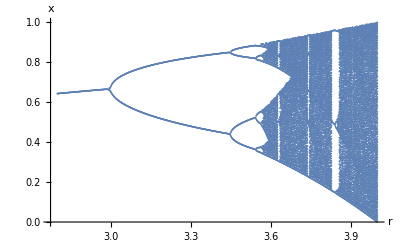

```mathematica
Table[{r,Union[Drop[NestList[r#(1-#)&,.1,600],300],SameTest->(Abs[#1-#2]<10^-2&)]},{r,2.8,4,0.001}];
%//Map[Thread,#]&//Flatten[#,1]&;
%//ListPlot[#,AxesLabel->{r,x},PlotRange->All]&
```

1971: David Ruelle has discovered a strange attractor.

```mathematica
{ⅆx/ⅆt==-3(x-y),ⅆy/ⅆt==-x z+26.5 x-y,ⅆz/ⅆt==x y-z}
SCMAF[%,SCNDSolve,{All,{x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,400},MaxSteps->∞},
Thread,{All,Equal},Take->{2},
SCApplyFunc,{All,#[t]&},Level->{1},
SCApplyFunc,{All,ParametricPlot3D[#,{t,0,400},PlotPoints->1000,Axes->False,Boxed->False,PlotStyle->Thick,ColorFunction->(ColorData["SolarColors",#4]&)]&}]
```

{ⅆx/ⅆt==-3 (x-y),ⅆy/ⅆt==26.5 x-y-x z,ⅆz/ⅆt==x y-z}

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

-Graphics3D-

1975: Benoit Mandelbrot has discovered fractals.

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{-0.65+0.47ⅈ,-0.4+0.72ⅈ}]
```

-Graphics-